## Пересечение

This is a text cell.

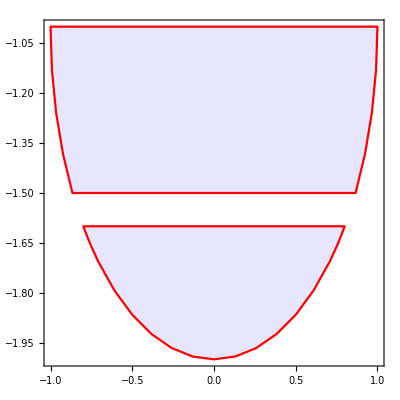

```mathematica
RegionDifference[
Disk[{0, -1}, 1, {-180.0°, 0 °}],
 Rectangle[{-1, -1.6}, {1, -1.5}]
];
rPlot=RegionPlot[%,BoundaryStyle->Red,PlotStyle->Lighter[Blue, 0.9]]
```

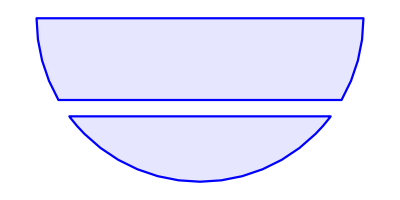

```mathematica
Graphics[{Red,rPlot[[1]]}]
```

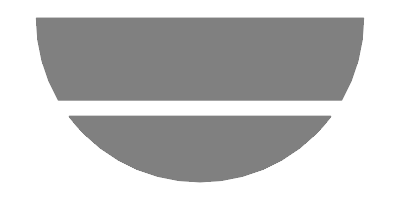

```mathematica
DeleteCases[rPlot[[1]],_Directive,-1];
Graphics[{Gray,EdgeForm[Directive[Thick,Red]],%}]
```

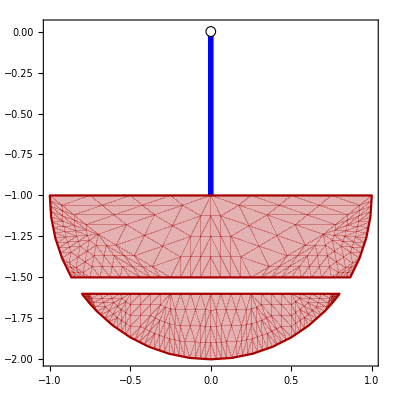

```mathematica
{Blue, Thickness[0.01], Line[{{0, 0}, {0, -1}}],
    Lighter[Blue, 0.7], EdgeForm[Directive[Thick, Blue]],
RegionPlot[RegionDifference[
Disk[{0, -1}, 1, {-180.0°, 0 °}],
 Rectangle[{-1, -1.6}, {1, -1.5}]
]][[1]],
    White, EdgeForm[Directive[Thick, Black]],
    Disk[{0, 0}, 0.03]
};
Graphics[%,Frame->True]
```

## Функция Manipulate

```mathematica
Manipulate[
Graphics[body1[φ,x], Frame -> True,PlotRange->{{-0.2,0.2},{-0.18,0.04}},ImageSize->500],
{φ,0,2π},{x,0,0.2}
]
```

## Загрузка внешних данных

Загрузка результатов расчётов из других программ (MATLAB, Python, Maple).
данные разделены пробелами

```mathematica
0.000 1.45641 5.445
0.010 1.49301 5.332
0.020 1.48611 5.156
...
1.100 2.45688 5.156
```

0.

0.0796073

0.153248

данные разделены запятыми

```mathematica
0.000,1.4564,15.445
0.010,1.4930,15.332
0.020,1.4861,15.156
...
1.100,2.4568,85.156
```

## Импорт из файла

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["motion.csv"];
Round[data[[1;;5]],0.01]
TableForm[%]
```

{{0.,0.2,0.,0.02,0.},{0.,0.2,-0.19,0.02,-0.04},{0.02,0.19,-0.76,0.02,-0.17},{0.03,0.18,-1.3,0.02,-0.28},{0.04,0.16,-1.79,0.01,-0.38}}

0. | 0.2 | 0. | 0.02 | 0.
0. | 0.2 | -0.19 | 0.02 | -0.04
0.02 | 0.19 | -0.76 | 0.02 | -0.17
0.03 | 0.18 | -1.3 | 0.02 | -0.28
0.04 | 0.16 | -1.79 | 0.01 | -0.38

```mathematica
Round[Transpose[data[[1;;5]]],0.01]
```

{{0.,0.,0.02,0.03,0.04},{0.2,0.2,0.19,0.18,0.16},{0.,-0.19,-0.76,-1.3,-1.79},{0.02,0.02,0.02,0.02,0.01},{0.,-0.04,-0.17,-0.28,-0.38}}

```mathematica
tmax=Max[Transpose[data][[1]]]
```

5.

## Интерполяция по таблице

Загруженные данные могут иметь неравномерный шаг по времени.

```mathematica
dataTable={{0,1},{0.5,2},{2,4},{4,10}};

f=Interpolation[dataTable]
```

InterpolatingFunction[{{0., 4.}}, <>]

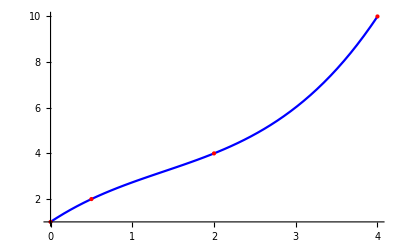

```mathematica
Show[{
Plot[f[x],{x,0,4},PlotStyle->Blue,BaseStyle->20],
ListPlot[dataTable,PlotStyle->{PointSize[Large],Red}]
}]
```

## Интерполяция по таблице

Линейная интерполяция

```mathematica
dataTable={{0,1},{0.5,2},{2,4},{4,10}};

f=Interpolation[dataTable,InterpolationOrder->1]
```

InterpolatingFunction[{{0., 4.}}, <>]

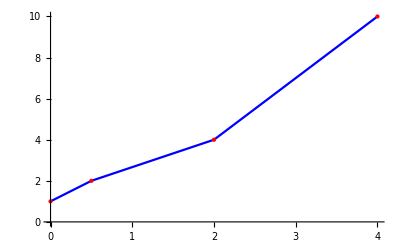

```mathematica
Show[{
Plot[f[x],{x,0,4},PlotStyle->Blue,BaseStyle->20],
ListPlot[dataTable,PlotStyle->{PointSize[Large],Red}]
}]
```

## Вектор-функция

Векторная функция скалярного аргумента

Interpolation[{{t_1, {x_1,y_1,z_1}},{t_2, {x_2,y_2,z_2}},...,{t_n, {x_n,y_n,z_n}}]

...но таблица “плоская”

```mathematica
Round[data[[1;;4]],0.001]
```

{{0.,0.2,0.,0.02,0.},{0.004,0.2,-0.192,0.02,-0.043},{0.016,0.194,-0.762,0.019,-0.169},{0.028,0.182,-1.301,0.016,-0.284}}

## Переформатирование таблицы

Приводим строки таблицы к нужной структуре

```mathematica
dataVec={#[[1]], #[[2 ;; 5]]} & /@ data;
```

# Подобный код на Питоне
dataVec = [ (x[0], (x[1], x[2], x[3], x[4]) ) for x in data ]

```mathematica
Round[dataVec[[1;;4]],0.01]
```

{{0.,{0.2,0.,0.02,0.}},{0.,{0.2,-0.19,0.02,-0.04}},{0.02,{0.19,-0.76,0.02,-0.17}},{0.03,{0.18,-1.3,0.02,-0.28}}}

```mathematica
inerpolatedData=Interpolation[dataVec];
```

```mathematica
inerpolatedData[1.5]
```

{0.154023,0.106255,0.00148632,-0.417274}